# Spencer Lyon

## Part 3 - Descriptive Analysis

Mean

### Point estimate for the mean of my variable. I am testing at the α=.95 level which corresponds to t_α values of {-2.086,2.086}

The point estimate for the average GDP in the United States in the past 20 years is 9.79957×10^12.
The range of expected values at the α=.95 level is {8.43653×10^12,1.11626×10^13}.

### Hypothesis test that the average US GDP is > 3.52 trillion $/yr. (that is the 2010 national budget)

H_0:μ=3.522e 12
H_a: μ < 3.522 e 12
α=.99
(x^--μ)/(√(s^2/n))~t(n-1) → t-score
(Mean[usgdp]-3.522*10^12)/(√(Variance[usgdp]/20))=9.60719

It is easy to see that 9.60719 is greater than -2.58 (See “Plot 1” at back) and therefore we are not in the rejection region. According to my data, at the  99% confidence level supports the null hypothesis that GDP is greater than the national budget.

The p-value associated with the test statistic 9.60719 is 4.99836×10^-9

### Probability that the expected range of values for US GDP is [8 trillion, 15 trillion]

{(Mean[usgdp]-15*10^12)/(√(Variance[usgdp]/20)),(Mean[usgdp]-8*10^12)/(√(Variance[usgdp]/20))}
{-7.95874,2.75406}
CDF[StudentTDistribution[19],2.75]=0.993632
CDF[StudentTDistribution[19],-7.95874]=9.04794×10^-8
0.993632-9.04794×10^-8=0.993632

This Shows that the probability that the real range of average US GDP in the past 20 years is [8 T, 15 T] is .993632. (See plot two attached at back)

Variance

### Point estimate of variance of US GDP in the past 20 years along with a confidence interval with α=.95.

The point estimate for variance is $8.53926×10^24.
The range of expected values for the variance is [5.38245×10^24,∞]

### Hypothesis test that the variance of US GDP is 10*10^24

H_o:σ^2=10E 24
H_a:σ^2> 10 E 24
α=.90, corresponding χ^2 value is 27.2036
((n-1)(S^2))/σ^2→ χ^2(n-1)=16.2246
1-CDF[ChiSquareDistribution[19],16.2246]=0.642244

In this case we are well outside of the rejection region (See “Plot 3”) and according to our data at the 90% confidence level we cannot reject the null hypothesis that the true variance is 10 *10^24.

The p-value associated with my test statistic is .642244.

### Probability that the real variance is in the following range: [5 *10^24,12 *10^24]

{((n-1)*(Variance[usgdp]))/(12*10^24),((n-1)*(Variance[usgdp]))/(5*10^24)}
{32.4492,13.5205}
CDF[ChiSquareDistribution[19],32.4492]=0.972199
CDF[ChiSquareDistribution[19],13.5205]=0.189108
.972199-0.189108=.783092

This Shows that the probability that the true variance is between [5 *10^24,12 *10^24] is.783092. (See “Plot 4” at back)

Proportion

### Point estimate and confidence interval for the proportion of (US consumption)/(US GDP) at an α level of .95 (corresponds to an α-value of 1.729)

p̂=Mean[usconsumption]/Mean[usgdp]=.845854
Standard Error=√((OverHat[(p](1-p̂)))/n)=0.0807418
Range of values = 1.729* SE=0.139603

The point estimate for the proportion (p̂) is .845854
The range of expected values at a .95 confidence level is [.1396, 1]

### Hypothesis Test that the true proportion of Total consumption (p) is >75% of US GDP

H_0:p̂=.75
H_a:p̂>.75
α=.90, α value is 1.328
(p̂-p)/(√((p(1-p))/n))~t (n-1)=0.0989976
1-CDF[StudentTDistribution[19],0.09899758551129752`]=0.461089

This shows that we are not in the rejection region (See “Plot 5”) and according to our data we cannot reject the null hypothesis that US consumption is =.75 US GDP at he .90 confidence level.

The p-value associated with my test statistic is .461089.

### Probability that the true proportion is in the range of [.5, .9]

{(p̂-.9)/(√((.5(.5))/20)),(p̂-.5)/(√((.5(.5))/20))}
{-0.484292, 3.09342}
CDF[StudentTDistribution[19],3.09342]=0.997009
CDF[StudentTDistribution[19],-.0484292]=0.48094
.997009-0.48094=.516069

This shows that the probability that the range true proportion of US consumption to US GDP is [.5, .9] is .516069. (See “Plot 6”)

## Part 4 - Comparative Analysis

Estimated Difference in means

### Point estimate and confidence interval for difference μ_1-μ_2 where μ_1 represents US GDP and μ_2 represents US Disposable Income at an α=.95 level (corresponds to an α ± 2.086).

The point estimate is 1.75143 * 10^12
The range of expected values is [2.16981×10^11,3.28588×10^12]

### Hypothesis test that GDP is more than 2 * 10^12 more than US Disposable income.

H_o:μ_1-μ_2=2 * 10^12
H_a:μ_1-μ_2≥ 2 * 10^12
α=.95, t_α value of 1.729
((Mean[usgdp]-Mean[usdisposable])-2 *10^12)/(√(Variance[usgdp]/20+Variance[usdisposable]/20))=-0.337914
1-CDF[StudentTDistribution[19],-0.33791429695559866`]=0.630434

According to our data at the α=.95 level we fail to reject the null hypothesis that  μ_1-μ_2=2 * 10^12. (See “Plot 7”)
The p-value associated with my test statistic is .630434

### Probability that the difference between GDP and Disposable Income is in the following range [0,2 *10^12]

{((Mean[usgdp]-Mean[usdisposable])-2 10^12)/(√(Variance[usgdp]/20+Variance[usdisposable]/20)),((Mean[usgdp]-Mean[usdisposable])-0)/(√(Variance[usgdp]/20+Variance[usdisposable]/20))}
{-0.337914, 2.38097}
CDF[StudentTDistribution[19],2.38097]=0.986057
CDF[StudentTDistribution[19],-0.337914]=0.369566
.986057-0.369566=.616491.

The probability that the true difference between average GDP and average disposable income is in the range [0,2 Trillion] is .616491. (See “Plot 8”)

Estimated Ratio of Variances

### A point estimate and confidence interval at the α=.10 level for the ratio of variances between US GDP from 1990 to 2009 and US GDP from 1929-1945. I chose this time period to compare to because it was a time of extreme variance/volatility in GDP due to the great depression and World War II. This means that σ_1^2/σ_2^2~F(20,17),where 1 corresponds to recent and 2 to depression.

The point estimate for the difference in variance for US GDP in the past 20 years to US GDP during the great  depression is 2852.23. This number is huge and surprised me and I think a lot of it might have to do with the fact that in today’s time we produce about 10x what they did in the 30’s.
The lower bound on our ratio with 90% confidence is .00065212.

### Hypothesis test that the ratio between variances is greater than 2500

H_0:σ^2/σ^2=2500
H_a:σ^2/σ^2>2500
α=.95, F-value of 1.86
((S^2)_1/(σ^2)_1)/((S^2)_(2/(σ^2)_2))~F(20,17)=((S^2)_1)/((S^2)_2)*((σ^2)_2)/((σ^2)_1)=1.14089
1-CDF[FRatioDistribution[20,17],1.1408934578734051`]=0.395334

This shows that according to our data at the 90% confidence level we cannot reject the null hypothesis. (See “Plot 9”)
The p-value associated with my test statistic is .395334

### Probability that the range of the variance ratio is between [1500,3000]

Variance[usgdp]/Variance[depressiongdp]*1/1500=1.90149
Variance[usgdp]/Variance[depressiongdp]*1/3000=.950745
CDF[FRatioDistribution[20,17],1.9014890964556752`]=.907213
CDF[FRatioDistribution[20,17],0.9507445482278376`]=0.452407
.907213-0.452407=454807

This shows that the probability that the ratio of true variances is in the range [1500,3000] is .454807 (See “Plot 10”)

Estimated difference in proportions

### Point estimate and confidence interval of the difference in the GDP growth rate and the money supply growth rate at the α=.95 level.

The point estimate is .0555.
The range of expected vales is [0,.096]

### Hypothesis test that the difference in proportions is 0.

H_0:p_1-p_2=0
H_a: p_1-p_2>0
α=.95
(Mean[newgdpgrowth]-Mean[newmoneyrate])/(√((Mean[newgdpgrowth]*(1-Mean[newgdpgrowth]))/(Variance[gdpgrowth]/20)+(Mean[newmoneyrate]*(1-Mean[newmoneyrate]))/(Variance[moneyrate]/20)))=.00103238
CDF[StudentTDistribution[19],0.0010323838839371249`]=.500406

According to our data we fail to reject the null hypothesis that there is a difference in the proportions at the .95 confidence level. (See “Plot 11”)
The p-value associated with my test statistic is .500406.

### Probability that the range of differences is between [-.05,.05]

{((Mean[newgdpgrowth]-Mean[newmoneyrate])+.05)/(√((Mean[newgdpgrowth]*(1-Mean[newgdpgrowth]))/(Variance[gdpgrowth]/20)+(Mean[newmoneyrate]*(1-Mean[newmoneyrate]))/(Variance[moneyrate]/20))),((Mean[newgdpgrowth]-Mean[newmoneyrate])-.05)/(√((Mean[newgdpgrowth]*(1-Mean[newgdpgrowth]))/(Variance[gdpgrowth]/20)+(Mean[newmoneyrate]*(1-Mean[newmoneyrate]))/(Variance[moneyrate]/20)))}
{-.0919602,.094025}
CDF[StudentTDistribution[19],0.09402495779256491`]=.536963
CDF[StudentTDistribution[19],-0.09196019002469066`]=0.463846
.536963-0.463846=.0731169

The probability that the proportions are between [.05,.05] us .0731169. (See “Plot 12”)

Plots

For all the plots the red line represents the rejection region, the dotted line represents the test statistic, the green lines represents the bounds on expected ranges.

```mathematica
Table[{plot1,plot2,plot3,plot4,plot5,plot6,plot7,plot8,plot9,plot10,plot11,plot12}]
```

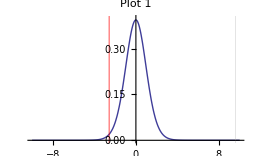
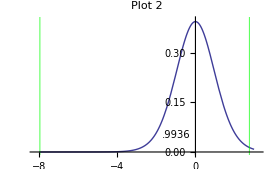
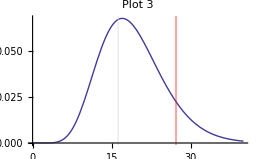
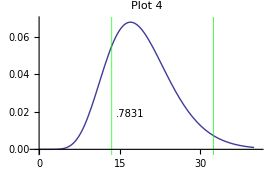
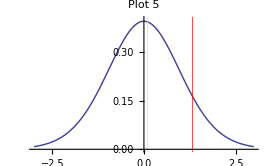
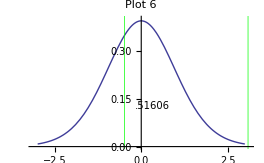
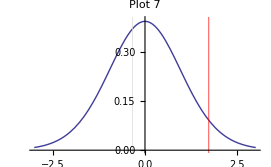
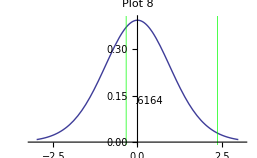

```mathematica
Table[{gdpincomeplot,moneygrowthplot}]
```